```mathematica
f[x_]:=Sin[x]-x/13
```

```mathematica
g[x_]:=x
h[x_] :=x/(1-x^2)
l[x_]:=x+10f[x]
```

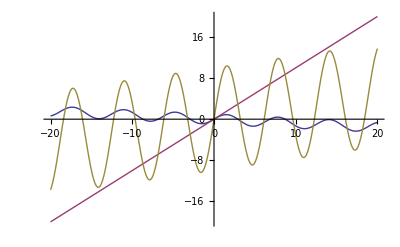

```mathematica
Plot[{f[x],g[x],l[x]},{x,-20,20}]
```

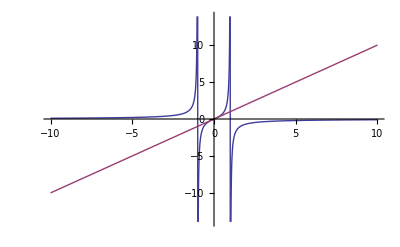

```mathematica
Plot[{h[x],g[x]},{x,-10,10}]
```

```mathematica
NSolve[f[x]==0,x,Reals]
```

{{x→-8.69239},{x→-6.83698},{x→-2.91541},{x→0.},{x→2.91541},{x→6.83698},{x→8.69239}}

```mathematica
NSolve[h[x]==0,x,Reals]
```

{{x→0.}}

```mathematica
l[l[l[l[l[l[l[l[l[l[l[-20]]]]]]]]]]]//N
```

8.91371